```mathematica
hbarc=.1973;
```

```mathematica
tau0Global=.4;
T0Global=.5;
qGlobal=.25;
cs2Global=1/3;

T0hatGlobal=(T0Global tau0Global ((1+qGlobal^2 tau0Global^2)^2)^(1/3))/(2^(2/3) (qGlobal tau0Global)^(2/3));
```

## Photon rate

### QGP rate at leading order

```mathematica
(* Number of colors *)
Nc=3;
(* Strong coupling constant *)
gs=Sqrt[4Pi(1/Pi)];
(* Electromagnetic coupling constant *)
ge=Sqrt[4Pi/137];

(* Temperature-stripped Debye mass *)
mDt[Nf_]:=gs Sqrt[(1+Nf/6)];
(* Temperature-stripped Debye mass *)
mInft:=gs/Sqrt[3];
(* Temperature-stripped thermal mass *)
mGammat[Nf_]:=1/Sqrt[2]*ge*Sqrt[Switch[Nf,1,(2/3)^2,2,(2/3)^2+(1/3)^2,3,(2/3)^2+2(1/3)^2,4,2(2/3)^2+2(1/3)^2,5,2(2/3)^2+3(1/3)^2,6,3(2/3)^2+3(1/3)^2]];

(* "Approximate, phenomenological fits" for C_{2->2}(x) and C_{brem}(x)+C_{annih}(x), as defined in [1] *)
ClpmAMY[Nf_,x_]:=Sqrt[1+Nf/6](.548Log[12.28+1/x]/x^(3/2)+.133x/Sqrt[1+x/16.27])
C22AMY[x_]:=(.041/x-.3615+1.01Exp[-1.35x])

(* C_{tot}(x) using the above approximate functions (and _not_ the numerical solution found in the previous section) *)
CtotAMY[Nf_,x_]:=ClpmAMY[Nf,x]+C22AMY[x]+Log[2 x]/2

(* Fermi-Dirac and Bose-Eistein distribution *)
nf[pu_,Tu_]:=1/(Exp[pu/Tu]+1)
nb[pu_,Tu_]:=1/(Exp[pu/Tu]-1)

FacA[Nf_,ku_,Tu_]:=2 (ge^2/4/Pi) (Nc Switch[Nf,1,(2/3)^2,2,(2/3)^2+(1/3)^2,3,(2/3)^2+2(1/3)^2,4,2(2/3)^2+2(1/3)^2,5,2(2/3)^2+3(1/3)^2,6,3(2/3)^2+3(1/3)^2] ) mInft^2 (Tu^2)/ku nf[ku,Tu]

(* Finally, Emission[Nf,ku,dku] is Subscript[ν, e](k) in the units chosen for T, k and p *)
dGammadkdyAMY[ku_?NumericQ,Tu_?NumericQ]:=FacA[3,ku,Tu] (Log[Sqrt[3]/gs]+CtotAMY[3,ku/Tu])/(2Pi)^3*ku/(hbarc)^4
```

```mathematica
(*With[{Tu=.5},LogPlot[{Exp[ku/Tu]dGammadkdyAMY[ku,Tu],Exp[ku/Tu]dGammadkdyAMYSimp[ku,Tu]},{ku,0.5,4.},PlotStyle->{Red,Directive[Green,Dashed],Blue,Black,Purple}]]*)
```

### Hadronic gas rate for a dominant channel (pi rho -> pi gamma)

```mathematica
FormFactor[ku_]:=With[{tpi=34.5096 ku^0.737-67.557 ku^0.7584+32.858 ku^0.7806},(2/(2-tpi))^2]
dGammadkdyPiRhoPiGamma[ku_?NumericQ,Tu_?NumericQ]:=FormFactor[ku](Tu^2.8 Exp[-(1.461 Tu^2.3094+0.727)/(2 Tu ku)^0.86+(0.566 Tu^1.4094-0.9957)ku/Tu])
```

### Rate to use in this notebook

```mathematica
(*dGammadkdyfast = Compile[{{ku, _Real},{Tu, _Real}},If[Tu>.18,dGammadkdyAMY[ku,Tu], dGammadkdyPiRhoPiGamma[ku,Tu]]];*)
dGammadkdyfast = Compile[{{ku, _Real},{Tu, _Real}},dGammadkdyAMY[ku,Tu]]
dGammadkdy[ku_?NumericQ,Tu_?NumericQ]:=dGammadkdyfast[ku,Tu]
(*dGammadkdy[ku_?NumericQ,Tu_?NumericQ]:=Tu^2 Exp[-ku/Tu]*)
```

CompiledFunction[…]

## Relativistic inviscid hydrodynamics: boost-invariant with cylindrical symmetry

```mathematica
(* u^\tau=cosh(alpha), u^r=sinh(alpha) *)
cylindricalBoostInvariantInviscidGeneral[tau0infm_,initCondT0Fct_,initCondkappaFct_,cs2Fct_]:=(

sols=NDSolve[{D[LogT[tau,r],tau]+Tanh[kappa[tau,r]]D[LogT[tau,r],r]==-(cs2Fct[Exp[LogT[tau,r]]]) (1/tau+Tanh[kappa[tau,r]]/r+Tanh[kappa[tau,r]] D[kappa[tau,r],tau]+D[kappa[tau,r],r]),D[kappa[tau,r],tau]+Tanh[kappa[tau,r]]D[kappa[tau,r],r]==-D[LogT[tau,r],r]/Cosh[kappa[tau,r]]^2+Tanh[kappa[tau,r]] cs2Fct[Exp[LogT[tau,r]]] (1/tau+Tanh[kappa[tau,r]]/r+Tanh[kappa[tau,r]] D[kappa[tau,r],tau]+D[kappa[tau,r],r]),LogT[tau0infm,r]==Log[initCondT0Fct[r]/hbarc],kappa[tau0infm,r]==initCondkappaFct[r]},{LogT,kappa},{tau,tau0infm,20.},{r,0.001,15},AccuracyGoal->5,PrecisionGoal->Infinity(*,InterpolationOrder->6*)];
tmplogTres=LogT/.sols[[1]];
tmpkappares=kappa/.sols[[1]];

Return[{tmplogTres,tmpkappares}];
)
```

### Checking with Gubser

```mathematica
TIdealGubser[tau_,r_,q_,T0hat_]:=T0hat (2 q tau)^(2/3)/(tau (1+2 q^2 (tau^2+r^2)+q^4 (tau^2-r^2)^2)^(1/3))
(*logTIdealGubser[tau_,r_,q_,T0hat_]:=Log[TIdealGubser[tau,r,q,T0hat]]*)
(* u^r[tau,r]=r H[tau,r]=Sinh[kappa[tau,r]] *)
HIdealGubser[tau_,r_,q_]:=(2 q^2 tau)/(√(1+q^4 (r^2-tau^2)^2+2 q^2 (r^2+tau^2)))
kappaGubser[tau_,r_,q_]:=ArcSinh[r HIdealGubser[tau,r,q]]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

{InterpolatingFunction[…],InterpolatingFunction[…]}

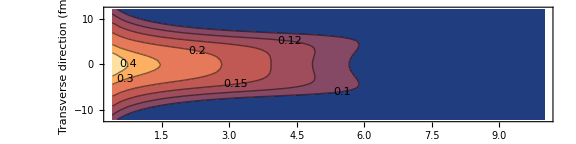

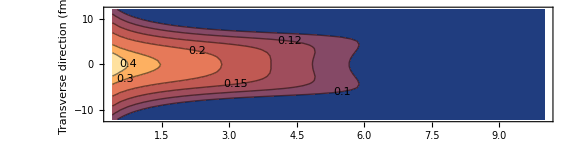

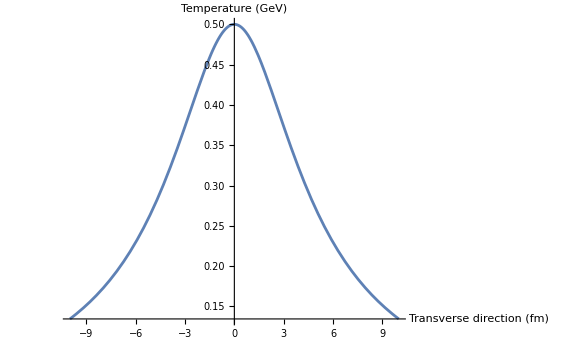

```mathematica
{logTresGubserNumerical,kappaGubserNumerical}=cylindricalBoostInvariantInviscidGeneral[tau0Global,Function[r,TIdealGubser[tau0Global,r,qGlobal,T0hatGlobal]],Function[r,kappaGubser[tau0Global,r,qGlobal]],Function[T,cs2Global]]

ContourPlot[{hbarc Exp[logTresGubserNumerical[tau,Abs[x]]]},{tau,tau0Global,10.},{x,-12,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All,AspectRatio->.25,ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14}]&),FrameLabel->{"τ (fm)","Transverse direction (fm)"},ImageSize->Large]

ContourPlot[hbarc TIdealGubser[tau,Abs[x],qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,10},{x,-12,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All,AspectRatio->.25,ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14}]&),FrameLabel->{"τ (fm)","Transverse direction (fm)"},ImageSize->Large]
Plot[hbarc TIdealGubser[tau0Global,Abs[x],qGlobal,T0hatGlobal/hbarc],{x,-10,10},AxesLabel->{"Transverse direction (fm)","Temperature (GeV)"},LabelStyle->{Black,FontSize->16}]
```

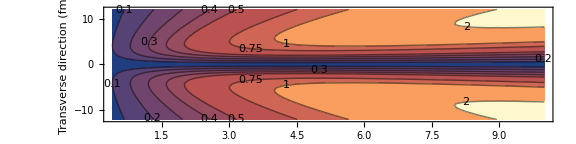

```mathematica
ContourPlot[{Abs[x] HIdealGubser[tau,Abs[x],qGlobal]},{tau,tau0Global,10.},{x,-12,12},Contours->{.1,.2,.3,.4,.5,.75,1.,2.},PlotRange->All,AspectRatio->.25,ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14}]&),FrameLabel->{"τ (fm)","Transverse direction (fm)"},ImageSize->Large]
```

#### How different is Gubser from Bjorken expansion? (that is, how much does the transverse expansion matter?)

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

{InterpolatingFunction[…],InterpolatingFunction[…]}

-Graphics-

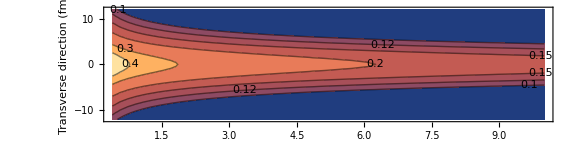

```mathematica
TIdealGubserInitBjorkenEvol[tau_,tau0_,r_,q_,T0hat_]:=TIdealGubser[tau0,r,q,T0hat](tau0/tau)^(1/3)

{logTresGubserNumerical,kappaGubserNumerical}=cylindricalBoostInvariantInviscidGeneral[tau0Global,Function[r,TIdealGubser[tau0Global,r,qGlobal,T0hatGlobal]],Function[r,kappaGubser[tau0Global,r,qGlobal]],Function[T,cs2Global]]

ContourPlot[hbarc TIdealGubser[tau,Abs[x],qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,10},{x,-12,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All,AspectRatio->.25,ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14}]&),FrameLabel->{"τ (fm)","Transverse direction (fm)"},ImageSize->Large]

ContourPlot[hbarc TIdealGubserInitBjorkenEvol[tau,tau0Global,Abs[x],qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,10},{x,-12,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All,AspectRatio->.25,ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14}]&),FrameLabel->{"τ (fm)","Transverse direction (fm)"},ImageSize->Large]
```

#### Pretty plot

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

{InterpolatingFunction[…],InterpolatingFunction[…]}

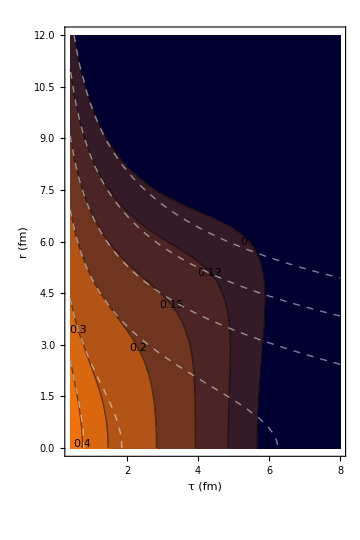

```mathematica
{logTresGubserNumerical,kappaGubserNumerical}=cylindricalBoostInvariantInviscidGeneral[tau0Global,Function[r,TIdealGubser[tau0Global,r,qGlobal,T0hatGlobal]],Function[r,kappaGubser[tau0Global,r,qGlobal]],Function[T,cs2Global]]

Show[ContourPlot[hbarc TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,8},{r,0,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All,AspectRatio->12/8.,ColorFunction->"RustTones",ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14},Background->Directive[White,Opacity[0.5]]]&),FrameLabel->{"τ (fm)","r (fm)"},ImageSize->Medium,FrameStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black]]
,
ContourPlot[hbarc TIdealGubserInitBjorkenEvol[tau,tau0Global,r,qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,8},{r,0,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All,AspectRatio->15/10.,FrameLabel->{"τ (fm)","r (fm)"},ImageSize->Medium,ContourShading->False,ContourStyle->Directive[Dashed,White,Thick],FrameStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black]]
]
```

```mathematica
(*Show[ContourPlot[r HIdealGubser[tau,r,qGlobal],{tau,tau0Global,8},{r,0,12},Contours->{.1,.2,.3,.4,.5,.75,1.,1.5,2.,3.},PlotRange->All,AspectRatio->12/8.,ColorFunction->ColorData[{"GrayTones","Reverse"}],ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14},Background->Directive[White,Opacity[0.5]]]&),FrameLabel->{"τ (fm)","r (fm)"},ImageSize->Medium,FrameStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black]],
ContourPlot[hbarc TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,8},{r,0,12},Contours->{.15},ContourStyle->Directive[Dashed,Blue,Thick],PlotRange->All,AspectRatio->12/8.,ContourShading->False,FrameLabel->{"τ (fm)","r (fm)"},ImageSize->Medium,FrameStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black]]]*)
```

```mathematica
(*Show[ContourPlot[r HIdealGubser[tau,r,qGlobal]/Sqrt[1+(r HIdealGubser[tau,r,qGlobal])^2],{tau,tau0Global,8},{r,0,12},Contours->{.1,.2,.3,.4,.5,.6,.7,.8,.9,1.},PlotRange->All,AspectRatio->12/8.,ColorFunction->ColorData[{"GrayTones","Reverse"}],ContourLabels->(Text[#3,{#1,#2},BaseStyle->{FontSize->14},Background->Directive[White,Opacity[0.5]]]&),FrameLabel->{"τ (fm)","r (fm)"},ImageSize->Medium,FrameStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black]],
ContourPlot[hbarc TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc],{tau,tau0Global,8},{r,0,12},Contours->{.15},ContourStyle->Directive[Dashed,Blue,Thick],PlotRange->All,AspectRatio->12/8.,ContourShading->False,FrameLabel->{"τ (fm)","r (fm)"},ImageSize->Medium,FrameStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black]]]*)
```

## Theoretical calculation of photon energy spectra

```mathematica
(* Exact temperature integration, exact spatial rapidity and monentum phi integration *)
exactCylindrical[tau0_?NumericQ,tauf_?NumericQ,Tf_?NumericQ,logTField_,HField_,kT_?NumericQ]:=(
1/(2Pi)NIntegrate[2 Pi r tau dGammadkdy[kT(Cosh[etas] Sqrt[1+(r HField[tau,r])^2]-(r HField[tau,r]) Cos[phi]),hbarc Exp[logTField[tau,r]]]HeavisideTheta[hbarc Exp[logTField[tau,r]]-Tf],{etas,-Infinity,Infinity},{phi,0,2Pi},{r,0,20.},{tau,tau0,tauf},AccuracyGoal->10,PrecisionGoal->Infinity,MinRecursion->10,MaxRecursion->30,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
)

(* Exact temperature integration, exact spatial rapidity and momentum phi integration *)
exactTCylindrical[tau0_?NumericQ,Tf_?NumericQ,logTField_,HField_,kT_?NumericQ]:=(
(* Restrict the domain of integration by noting that the point at r=0 will be the last to reach the minimum temperature Tf *)
taumax=tau/.Flatten[NSolve[hbarc Exp[logTField[tau,0]]==Tf,tau,Reals]];

1/(2Pi)NIntegrate[2 Pi r tau dGammadkdy[kT(Cosh[etas] Sqrt[1+(r HField[tau,r])^2]-(r HField[tau,r]) Cos[phi]),hbarc Exp[logTField[tau,r]]]HeavisideTheta[hbarc Exp[logTField[tau,r]]-Tf],{etas,-Infinity,Infinity},{phi,0,2Pi},{r,0,20.},{tau,tau0,1.5*taumax},AccuracyGoal->10,PrecisionGoal->Infinity,MinRecursion->10,MaxRecursion->30,Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
)

(* Exact temperature integration, exact spatial rapidity and momentum phi integration *)
exactTCylindricalTRange[tau0_?NumericQ,Tmax_?NumericQ,Tmin_?NumericQ,logTField_,HField_,kT_?NumericQ]:=(
(* Restrict the domain of integration by noting that the point at r=0 will be the last to reach the minimum temperature Tf *)
taumax=tau/.Flatten[NSolve[hbarc Exp[logTField[tau,0]]==Tmin,tau,Reals]];

1/(2Pi)NIntegrate[2 Pi r tau dGammadkdy[kT(Cosh[etas] Sqrt[1+(r HField[tau,r])^2]-(r HField[tau,r]) Cos[phi]),hbarc Exp[logTField[tau,r]]]HeavisideTheta[hbarc Exp[logTField[tau,r]]-Tmin] HeavisideTheta[Tmax-hbarc Exp[logTField[tau,r]]],{etas,-Infinity,Infinity},{phi,0,2Pi},{r,0,20.},{tau,tau0,1.5*taumax},AccuracyGoal->10,PrecisionGoal->Infinity,MinRecursion->10,MaxRecursion->30,Method->{"GlobalAdaptive","MaxErrorIncreases"->30000}]
)


(* Exact volume formula *)
dVdTCylExact[TinGeV_,T0inGeV_,q_,tau0infm_]:=With[{T=TinGeV,T0=T0inGeV,tau0=tau0infm},(*1/(2 q^3 T^4)π T0^3 tau0 (1+q^2 tau0^2)^2 (-ArcSin[(2 q (T/T0)^(3/2) tau0)/(1+q^2 tau0^2)]+ArcSin[(2 q)/((1+q^2 tau0^2) √((T0^3 tau0)/(T^3 Root[-T0^3 tau0-2 q^2 T0^3 tau0^3-q^4 T0^3 tau0^5+T^3 #1+2 q^2 T^3 #1^3+q^4 T^3 #1^5&,1]^3)))])*)
(*1/(2 q^3 T^4)π T0^3 tau0 (1+q^2 tau0^2)^2 (ArcCsc[1/2 T0 (1+q^2 tau0^2) √((q T0 tau0)/(T^3 Root[(-q T0^3 tau0 (1+q^2 tau0^2)^2)/T^3+ #1 (1+#1^2)^2&,1]^3))]-ArcSin[(2 q (T/T0)^(3/2) tau0)/(1+q^2 tau0^2)])*)
With[{w=(2 q (T/T0)^(3/2) tau0)/(1+q^2 tau0^2),x=1/(√((q^3 tau0^3)/(Root[(-q T0^3 tau0 (1+q^2 tau0^2)^2)/T^3+ #1 (1+#1^2)^2&,1]^3)))},1/(2 q^3 T^4)π T0^3 tau0 (1+q^2 tau0^2)^2 If[w>(q tau0)^(3/2), (ArcSin[x w]-ArcSin[w]),ArcCos[w]]

]]


exactVolumeNoFlow[tau0_?NumericQ,T0_?NumericQ,q_?NumericQ,Tf_?NumericQ,kT_?NumericQ]:=(
NIntegrate[dVdTCylExact[T,T0,q,tau0] dGammadkdy[kT(Cosh[etas]),T],{etas,-Infinity,Infinity},{T,Tf,T0},AccuracyGoal->10,PrecisionGoal->Infinity]
)
exactVolumeNoFlowApproxEta[tau0_?NumericQ,T0_?NumericQ,q_?NumericQ,Tf_?NumericQ,kT_?NumericQ]:=(
NIntegrate[Sqrt[2 Pi T/kT]dVdTCylExact[T,T0,q,tau0] dGammadkdy[kT,T],{T,Tf,T0},AccuracyGoal->10,PrecisionGoal->Infinity]
)

(* Approximate volume formula *)
dVdTCylHighTApprox[TinGeV_,T0inGeV_,q_,tau0infm_]:=1/(2 q^3 TinGeV^4)π T0inGeV^3 tau0infm (1+q^2 tau0infm^2)^2 (2 q (-(TinGeV/T0inGeV)^(3/2)+T0inGeV^3/TinGeV^3) tau0infm) 
dVdTCylLowTApprox[TinGeV_,T0inGeV_,q_,tau0infm_]:=(π T0inGeV^3 tau0infm (1+q^2 tau0infm^2)^2)/(2 q^3 TinGeV^4) π/2


(* Integrate over eta_s assuming approximate exponential dependence of the rate *)
approxHighTVolumeApproxEta[tau0_?NumericQ,T0_?NumericQ,q_?NumericQ,Tf_?NumericQ,kT_?NumericQ]:=(
NIntegrate[Sqrt[2 Pi T/kT]dVdTCylHighTApprox[T,T0,q,tau0] dGammadkdy[kT,T],{T,Tf,T0},AccuracyGoal->10,PrecisionGoal->Infinity]
)

(* Integrate over T assuming approximate T^2 exp(-kT/T) dependence of the rate *)
approxHighTVolumeApproxEtaRateInt[tau0_?NumericQ,T0_?NumericQ,q_?NumericQ,Tf_?NumericQ,kT_?NumericQ]:=(
(Exp[kT/T0]/T0^2dGammadkdy[kT,T0])1/(√kT q^2)√2 π^(3/2) T0^(3/2) (tau0+q^2 tau0^3)^2 (-ⅇ^(-kT/T0) T0+ⅇ^(-kT/Tf) Tf+1/(8 kT^(7/2))T0^(9/2) (-1/(T0 Tf)^(5/2)2 ⅇ^(-kT (1/T0+1/Tf)) √kT (-ⅇ^(kT/Tf) (4 kT^2+10 kT T0+15 T0^2) Tf^(5/2)+ⅇ^(kT/T0) T0^(5/2) (4 kT^2+10 kT Tf+15 Tf^2))-15 √π Erf[√(kT/T0)]+15 √π Erf[√(kT/Tf)])-kT ExpIntegralEi[-kT/T0]+kT ExpIntegralEi[-kT/Tf])
)
approxHighTVolumeApproxEtaRateIntSimp[tau0_?NumericQ,T0_?NumericQ,q_?NumericQ,Tf_?NumericQ,kT_?NumericQ]:=(
(Exp[kT/T0]/T0^2dGammadkdy[kT,T0])1/(√kT q^2)√2 π^(3/2) T0^(3/2) (tau0+q^2 tau0^3)^2 (ⅇ^(-kT (1/T0)) (9  T0^3))/(2 kT^2)
)
```

## Theoretical calculation of photon energy spectra - diagnostic

### Evaluating the effect of the transverse flow velocity

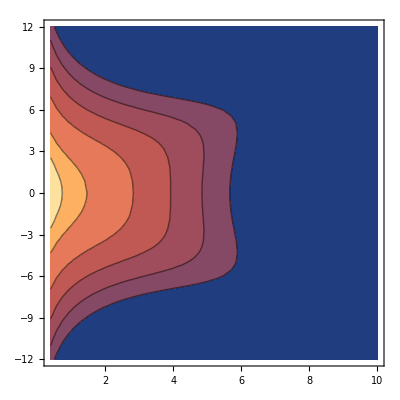

```mathematica
HresZero[tau_,r_]:=0

ContourPlot[{hbarc TIdealGubser[tau,Abs[r],qGlobal,T0hatGlobal/hbarc]},{tau,tau0Global,10},{r,-12,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All]
```

```mathematica
kTList=Table[kT,{kT,0.5,6.5,.5}];
TfGlobal=.1;
dNwithflow=ParallelTable[{kT,exactTCylindrical[tau0Global,TfGlobal,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],Function[{tau,r},HIdealGubser[tau,r,qGlobal]],kT]},{kT,kTList}];
(*dNwithoutflow=ParallelTable[{kT,0(*exactTCylindrical[tau0Global,TfGlobal,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],HresZero,kT]*)},{kT,kTList}];*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0171454 and 0.0000708078 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00406554 and 0.0000103441 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00103457 and 1.49388×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0795666 and 0.000472932 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000278243 and 2.8953×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000781402 and 4.43096×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000227244 and 6.77793×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.08008×10^-6 and 2.93594×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.7971×10^-6 and 2.93733×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.3973 and 0.0445866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.429365 and 0.00333982 for the integral and error estimates.

```mathematica
dNExactVolumeNoFlow=ParallelTable[{kT,exactVolumeNoFlow[tau0Global,T0Global,qGlobal,TfGlobal,kT]},{kT,kTList}];
dNExactVolumeNoFlowApproxEta=ParallelTable[{kT,exactVolumeNoFlowApproxEta[tau0Global,T0Global,qGlobal,TfGlobal,kT]},{kT,kTList}];
dNApproxHighTVolumeApproxEta=ParallelTable[{kT,approxHighTVolumeApproxEta[tau0Global,T0Global,qGlobal,TfGlobal,kT]},{kT,kTList}];
dNApproxHighTVolumeApproxEtaSimp=ParallelTable[{kT,approxHighTVolumeApproxEtaRateIntSimp[tau0Global,T0Global,qGlobal,TfGlobal,kT]},{kT,kTList}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14765}. NIntegrate obtained 0.501577 and 3.14343×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in T near {T} = {0.14765}. NIntegrate obtained 0.0510719 and 6.57154×10^-10 for the integral and error estimates.

{{0.5,1.31329},{1.,0.0599942},{1.5,0.00873489},{2.,0.00181146},{2.5,0.000435814},{3.,0.000113867},{3.5,0.0000314015},{4.,9.00102×10^-6},{4.5,2.6565×10^-6},{5.,8.02157×10^-7},{5.5,2.46724×10^-7},{6.,7.70469×10^-8},{6.5,2.43685×10^-8}}

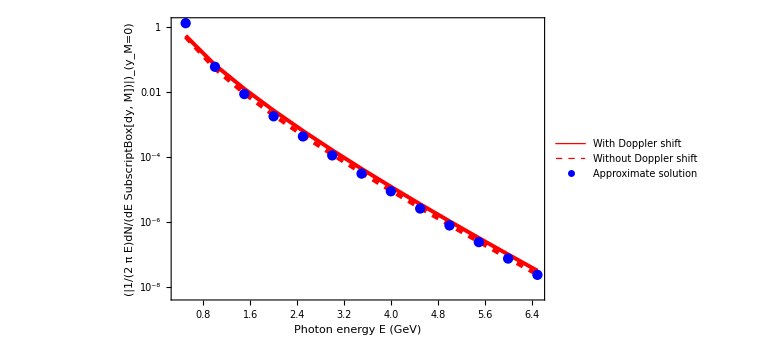

```mathematica
ListLogPlot[{dNwithflow,dNExactVolumeNoFlow,dNApproxHighTVolumeApproxEtaSimp},PlotStyle->{Directive[Red,Thickness[.005]],Directive[Red,Thickness[.005],Dashed],Directive[Blue,Thickness[.01]],Directive[Green,Thickness[.01],Dotted],Directive[Black,Thickness[.01],Dotted]},Joined->{True,True,False,True,True},
PlotLegends->Placed[{ "With Doppler shift","Without Doppler shift","Approximate solution"},{0.69,0.8}],
LabelStyle->Directive[FontFamily->"CMU",FontSize->18,FontColor->Black],FrameLabel->{"Photon energy E (GeV)",(|"1/(2  π E)dN/(dE SubscriptBox[dy, M])"|)_("y_M=0")},Frame->True,Axes->False,ImageSize->Large,FrameStyle->Directive[FontFamily->"CMU",FontSize->20,FontColor->Black],PlotRange->All]
```

```mathematica
kTList=Table[kT,{kT,0.5,6.5,1.}];
dNabove200WithFlow=ParallelTable[{kT,exactTCylindricalTRange[tau0Global,.5,.200,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],Function[{tau,r},HIdealGubser[tau,r,qGlobal]],kT]},{kT,kTList}];
dNabove200WithoutFlow=ParallelTable[{kT,exactTCylindricalTRange[tau0Global,.5,.200,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],HresZero,kT]},{kT,kTList}];
dNbelow200WithFlow=ParallelTable[{kT,exactTCylindricalTRange[tau0Global,.2,TfGlobal,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],Function[{tau,r},HIdealGubser[tau,r,qGlobal]],kT]},{kT,kTList}];
dNbelow200WithoutFlow=ParallelTable[{kT,exactTCylindricalTRange[tau0Global,.2,TfGlobal,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],HresZero,kT]},{kT,kTList}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00362449 and 0.0000157389 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0002652 and 3.73627×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000223059 and 1.17903×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.06587×10^-6 and 4.2611×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0619829 and 0.000902384 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.91609 and 0.0600402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00292085 and 2.84976×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0547166 and 0.000514436 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000207695 and 1.81145×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.9217 and 0.0594436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.48996×10^-8 and 7.22909×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000468149 and 0.0000293958 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000137591 and 7.66968×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.39395×10^-7 and 1.92087×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0198335 and 0.00178922 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.61937 and 0.12772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.59243×10^-8 and 2.01158×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000149385 and 3.13047×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00371997 and 0.000704857 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 30000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.38145 and 0.101668 for the integral and error estimates.

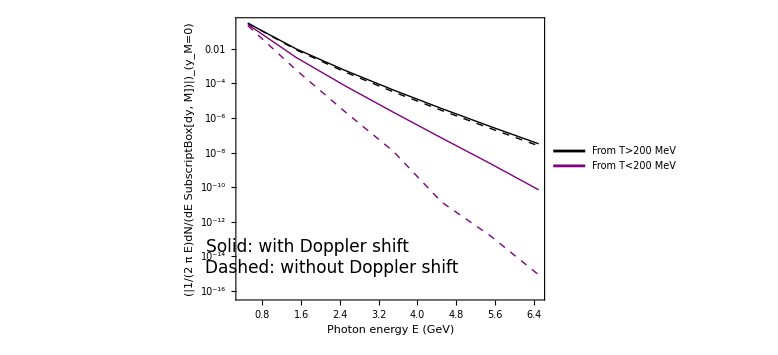

```mathematica
ListLogPlot[{dNabove200WithFlow,dNabove200WithoutFlow,dNbelow200WithFlow,dNbelow200WithoutFlow},PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed,Thick],Directive[Purple,Thick],Directive[Purple,Dashed,Thick]},Joined->True,PlotLegends->Placed[{"From T>200 MeV", None,"From T<200 MeV", None},{.25,0.4}],LabelStyle->Directive[FontFamily->"CMU",FontSize->17,FontColor->Black],FrameLabel->{"Photon energy E (GeV)",(|"1/(2  π E)dN/(dE SubscriptBox[dy, M])"|)_("y_M=0")},Frame->True,Axes->False,ImageSize->Large,FrameStyle->Directive[FontFamily->"CMU",FontSize->20,FontColor->Black],PlotRange->All,Epilog->{Text[Style["Solid: with Doppler shift         \nDashed: without Doppler shift",17],Scaled[{0.31,0.15}]]}]
```

#### Volume

```mathematica
T0=T0Global;
tau0=tau0Global;
q=qGlobal;

LogLogPlot[{dVdTCylExact[T,T0,q,tau0],dVdTCylHighTApprox[T,T0,q,tau0],dVdTCylLowTApprox[T,T0,q,tau0]},{T,.1,T0Global},PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed,Thick],Directive[Black,DotDashed,Thick],Directive[Green,Dotted,Thick]},FrameLabel->{"Temperature (GeV)","dV/dT (fm^4 GeV^-1)"},Frame->True,Axes->False,ImageSize->Large,FrameStyle->Directive[FontFamily->"CMU",FontSize->21,FontColor->Black],PlotLegends->Placed[{"Exact (Eq. 10)", "Approximate high T (Eq. 13)","Approximate low T (Eq. 14)"},{0.25,0.2}],LabelStyle->Directive[FontFamily->"CMU",FontSize->19,FontColor->Black,PlotRange->{{.1,.5},{10^-6,10}}]]


Clear[T0,tau0,q];
```

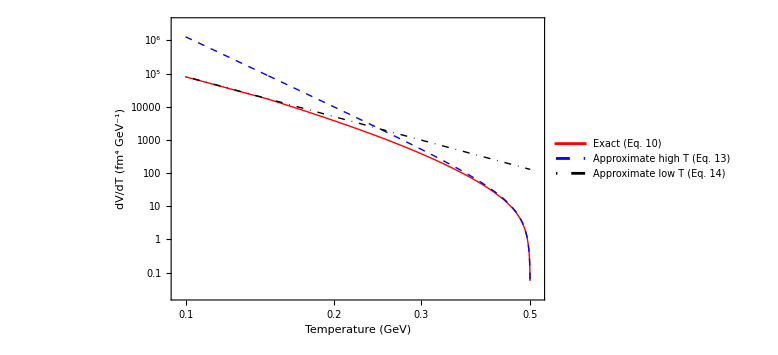

```mathematica
(*With[{T0=T0Global,q=qGlobal,tau0=tau0Global},ParallelTable[With[{exact=dVdTCylExact[T,T0,q,tau0],approxHigh=dVdTCylHighTApprox[T,T0,q,tau0],approxLow=dVdTCylLowTApprox[T,T0,q,tau0]},{T,approxHigh/exact,approxLow/exact}],{T,.1,T0*.9999,(.9999T0-.1)/100}]]//TableForm*)
```

### What is the effect of the lower limit on the temperature integration?

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00100235 and 4.71893×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.362274 and 0.00371523 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000772094 and 1.10574×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0158772 and 0.0000320858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0166131 and 0.0000146629 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.40252 and 0.00344662 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00102137 and 1.13504×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000777664 and 5.09151×10^-9 for the integral and error estimates.

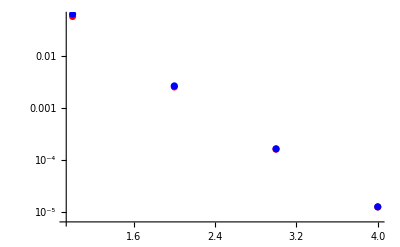

```mathematica
tau0Global=.4;
T0Global=.5;
qGlobal=.25;
T0hatGlobal=(T0Global tau0Global ((1+qGlobal^2 tau0Global^2)^2)^(1/3))/(2^(2/3) (qGlobal tau0Global)^(2/3));

ContourPlot[{hbarc TIdealGubser[tau,Abs[r],qGlobal,T0hatGlobal/hbarc]},{tau,tau0Global,10},{r,-12,12},Contours->{.1,.12,.15,.2,.3,.4,.5},PlotRange->All]

kTList=Table[kT,{kT,1,4,1.}];
dNwithTf150=ParallelTable[{kT,exactTCylindrical[tau0Global,.15,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],Function[{tau,r},HIdealGubser[tau,r,qGlobal]],kT]},{kT,kTList}];
dNwithTf120=ParallelTable[{kT,exactTCylindrical[tau0Global,.12,Function[{tau,r},Log[TIdealGubser[tau,r,qGlobal,T0hatGlobal/hbarc]]],Function[{tau,r},HIdealGubser[tau,r,qGlobal]],kT]},{kT,kTList}];
Show[ListLogPlot[dNwithTf150,PlotStyle->Red],ListLogPlot[dNwithTf120,PlotStyle->Blue]]
```

```mathematica
dNwithTf150/dNwithTf120
```

{{1.,0.900016},{1.,0.955708},{1.,0.981381},{1.,0.992838}}

### Teff plot

```mathematica
TeffSlope[T0_,W_]:=T0/(1+5/2 T0/W )
```

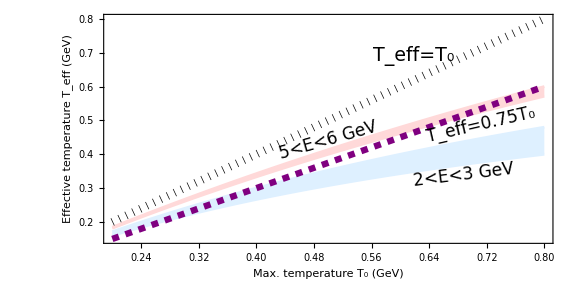

```mathematica
Plot[{TeffSlope[T0,2.],TeffSlope[T0,3.],TeffSlope[T0,5.],TeffSlope[T0,6.],0.75*T0,T0},{T0,.2,.8},PlotRange->All,PlotStyle->{LightBlue,LightBlue,LightRed,LightRed,Directive[Purple,Dashed,Thickness[.008]],Directive[Black,Dotted,Thickness[.01]]},Filling->{1->{{2},{LightBlue,White}},3->{{4},{LightRed,White}}},Epilog->{Text[Style[Rotate["2<E<3 GeV",7 Degree],17],Scaled[{0.8,0.3}]],Text[Style[Rotate["5<E<6 GeV",16 Degree],17],Scaled[{0.5,0.45}]],Text[Style["T_eff=T_0",19],Scaled[{0.69,0.82}]],Text[Style[Rotate["T_eff=0.75T_0",13 Degree],17],Scaled[{0.84,0.52}]]},AspectRatio->0.5,Frame->True,FrameLabel->{"Max. temperature T_0 (GeV)","Effective temperature\nT_eff (GeV)"},ImageSize->Large,FrameStyle->Directive[FontFamily->"CMU",FontSize->20,FontColor->Black]]
```